```mathematica
(* Oka's data *)
data ={{0.8,1.75},{1.1,1.65},{1.3,1.6},{1.5,1.5},{1.8,1.1},{2.2,0.6}};
```

```mathematica
(* Fit of modified Cam-Clay*)
modCamClay=NonlinearModelFit[data,{a √(p(b-p)),b>2.2},{a,b},p];
(* Fit of Cam-Clay*)
camClay=NonlinearModelFit[data,{a p Log[b/p]},{a,b},p];
```

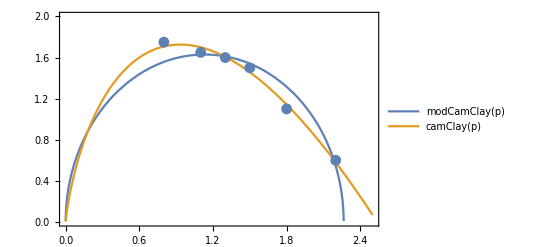

```mathematica
Show[
Plot[{modCamClay[p],camClay[p]},{p,-1,2.5},PlotLegends->"Expressions"], (* Plot fits *)
ListPlot[data], (* Plot data *)
Frame->True,
PlotRange->{{0,2.5},{0,2}}
]
```

```mathematica
(* Show fit results in human readable form *)
Normal[camClay]
```

1.8493 p Log[2.53708/p]

```mathematica
Normal[modCamClay]
```

1.43882 √((2.26473-p) p)